```mathematica
DistanceToMemory = 100/40
```

5/2

```mathematica
visibility[maxvalue_,minvalue_] := N[(maxvalue-minvalue)/(maxvalue+minvalue)]
```

```mathematica
visibilityunc[1.087,1.121,0.1228,0.1205]
uncvisibility2[1.087,1.121,0.1228,0.1205]
```

visibilityunc[1.087,1.121,0.1228,0.1205]

uncvisibility2[1.087,1.121,0.1228,0.1205]

```mathematica
VDUUB = AAA ((MMM-III)-DDD)/((MMM-III)+DDD)
```

(AAA (-DDD-III+MMM))/(DDD-III+MMM)

```mathematica
FindFit[doubleSlitVisibilities,VDUUB,{AAA,III,DDD},MMM]
```

{AAA→0.889416,III→3.67664,DDD→6.64674}

```mathematica
doubleSlitVisibilities = {{5*DistanceToMemory,0.14725928770279353},{7.5*DistanceToMemory,0.30194977986356375},{10*DistanceToMemory,0.4364037101662228},{12.5*DistanceToMemory,0.555312618256738},{15*DistanceToMemory,0.6144829800899165},{20*DistanceToMemory,0.7028137115657748},{30*DistanceToMemory,0.7720332695536726},{40*DistanceToMemory,0.7779378802433558},{50*DistanceToMemory,0.8014930853016766},{60*DistanceToMemory,0.7901549991483563},{70*DistanceToMemory,0.8126739806779104},{80*DistanceToMemory,0.807422436385155}}
doubleSlitVisibilitiesEbar = {{{5*DistanceToMemory,0.14725928770279353},ErrorBar[0.028661093263093823]},{{7.5*DistanceToMemory,0.30194977986356375},ErrorBar[0.02093537328913231]},{{10*DistanceToMemory,0.4364037101662228},ErrorBar[0.038283847087534184]},{{12.5*DistanceToMemory,0.555312618256738},ErrorBar[0.020859221713538267]},{{15*DistanceToMemory,0.6144829800899165},ErrorBar[0.02384184697194225]},{{20*DistanceToMemory,0.7028137115657748},ErrorBar[0.025872064217915547]},{{30*DistanceToMemory,0.7720332695536726},ErrorBar[0.0398349295895124]},{{40*DistanceToMemory,0.7779378802433558},ErrorBar[0.02]},{{50*DistanceToMemory,0.8014930853016766},ErrorBar[0.02]},{{60*DistanceToMemory,0.7901549991483563},ErrorBar[0.02]},{{70*DistanceToMemory,0.8126739806779104},ErrorBar[0.02]},{{80*DistanceToMemory,0.807422436385155},ErrorBar[0.02]}}
```

{{25/2,0.147259},{18.75,0.30195},{25,0.436404},{31.25,0.555313},{75/2,0.614483},{50,0.702814},{75,0.772033},{100,0.777938},{125,0.801493},{150,0.790155},{175,0.812674},{200,0.807422}}

{{{25/2,0.147259},ErrorBar[0.0286611]},{{18.75,0.30195},ErrorBar[0.0209354]},{{25,0.436404},ErrorBar[0.0382838]},{{31.25,0.555313},ErrorBar[0.0208592]},{{75/2,0.614483},ErrorBar[0.0238418]},{{50,0.702814},ErrorBar[0.0258721]},{{75,0.772033},ErrorBar[0.0398349]},{{100,0.777938},ErrorBar[0.02]},{{125,0.801493},ErrorBar[0.02]},{{150,0.790155},ErrorBar[0.02]},{{175,0.812674},ErrorBar[0.02]},{{200,0.807422},ErrorBar[0.02]}}

```mathematica
Needs["ErrorBarPlots`"]
```

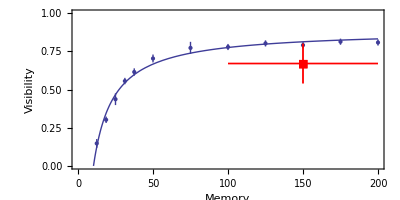

```mathematica
Show[Plot[-0.8894162739256767(6.646738318853071-(x-3.6766383665537212))/(6.646738318853071+(x-3.6766383665537212)),{x,5,200},Frame->True,PlotRange->{{0,200},{0,1}}, AspectRatio->0.5,BaseStyle->{FontFamily->"Times",FontSize->14}, FrameLabel->{"Memory","Visibility"}],ErrorListPlot[doubleSlitVisibilitiesEbar],ErrorListPlot[{{{150,0.67},ErrorBar[50,0.13]}},PlotMarkers->■,PlotStyle->Red]]
```

```mathematica
FindFit[doubleSlitVisibilities,VDUUB,{AAA,III,DDD},MMM]
```

{AAA→0.889416,III→3.67664,DDD→6.64674}

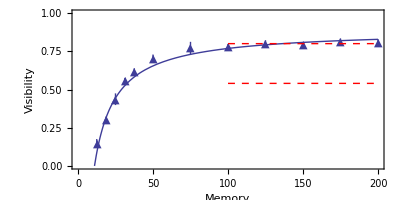

```mathematica
Show[Plot[-0.8894162739256767(7-(x-4))/(7+(x-4)),{x,0,200},Frame->True,PlotRange->{{0,200},{0,1}}, AspectRatio->0.5,BaseStyle->{FontFamily->"Times",FontSize->14}, FrameLabel->{"Memory","Visibility"}],ErrorListPlot[doubleSlitVisibilitiesEbar,PlotMarkers->▲],Plot[0.67+0.13,{x,100,200},PlotStyle->{Red,Dashed}],Plot[0.67-0.13,{x,100,200},PlotStyle->{Red,Dashed}]]
```

```mathematica
visibility[1.108,0.1224]
```

0.80104

```mathematica
Fit[doubleSlitVisibilities,{-(1-(x-4))/(1+(x-4))},x]
```

(0.651877 (-5+x))/(-3+x)

```mathematica
Fit[doubleSlitVisibilities,{ArcTan[(x-4)/2]},x]
```

0.449141 ArcTan[1/2 (-4+x)]

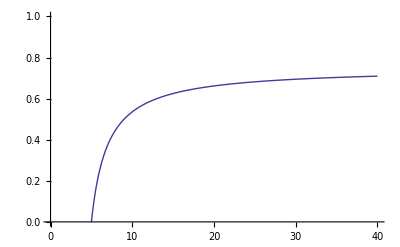

```mathematica
Plot[-0.75(1-(x-4))/(1+(x-4)),{x,4,40},PlotRange->{{0,40},{0,1}}]
```

```mathematica
kuptku = {}
Do[AppendTo[kuptku,"/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitPhaseCosC40W2M"<> ToString[FNUM] <> ".dat"] ,{FNUM,{1,3,5,7,40}}]
kuptku
```

{}

{/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitPhaseCosC40W2M1.dat,/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitPhaseCosC40W2M3.dat,/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitPhaseCosC40W2M5.dat,/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitPhaseCosC40W2M7.dat,/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitPhaseCosC40W2M40.dat}

```mathematica
visibilityunc[maxvalueA_, maxvalueB_,minvalueA_,minvalueB_] := N[((maxvalueA+maxvalueB)-(minvalueA+minvalueB))/((maxvalueA+maxvalueB)+(minvalueA+minvalueB))]
```

```mathematica
visibilityunc[0.5979,0.5972,0.4314,0.4569]
```

0.147259

```mathematica
uncvisibility[maxvalueA_, maxvalueB_,minvalueA_,minvalueB_]:=N[2visibilityunc[maxvalueA, maxvalueB,minvalueA,minvalueB]((Abs[(maxvalueA-maxvalueB)]+Abs[(minvalueA-minvalueB)])/((maxvalueA+maxvalueB)-(minvalueA+minvalueB))+(Abs[(maxvalueA-maxvalueB)]+Abs[(minvalueA-minvalueB)])/((maxvalueA+maxvalueB)+(minvalueA+minvalueB)))]
```

```mathematica
uncvisibility[0.5979,0.5972,0.4314,0.4569]
```

0.0288549

```mathematica
uncvisibility2[maxvalueA_, maxvalueB_,minvalueA_,minvalueB_]:=N[(Max[maxvalueA, maxvalueB]-Min[minvalueA,minvalueB])/(Max[maxvalueA, maxvalueB]+Min[minvalueA,minvalueB])-(Min[maxvalueA, maxvalueB]-Max[minvalueA,minvalueB])/(Min[maxvalueA, maxvalueB]+Max[minvalueA,minvalueB])]
```

```mathematica
uncvisibility2[0.5979,0.5972,0.4314,0.4569]
```

0.0286611

```mathematica
visibility[13,2]
```

0.733333